```mathematica
F[n_] := Sum[ n/x,{x,2,n}]
```

```mathematica
N[F[100]]
```

418.738

```mathematica
F2[n_] := n Sum[ 1/x,{x,2,n}]
```

```mathematica
N[F2[100]]
```

418.738

```mathematica
F3[x_] := x( Floor[x]/x-Floor[2]/2+Integrate[ Floor[u]/u^2,{u,2,x}])
```

```mathematica
N[F3[100]]
```

368.738

```mathematica
T1[x_] := Sum[ 1/n,{n,1,x}]
T2[x_] := Floor[x]/x + Integrate[ Floor[u]/u^2,{u,1,x}]
T1[100]
T2[100]
```

14466636279520351160221518043104131447711/2788815009188499086581352357412492142272

14466636279520351160221518043104131447711/2788815009188499086581352357412492142272

```mathematica
T1[x_] := x Sum[ 1/n,{n,2,x}]
T2[x_] := x (Floor[x]/x -Floor[2-1]/2+ Integrate[ Floor[u]/u^2,{u,2,x}])
N[T1[100]]
N[T2[100]]
```

418.738

418.738

```mathematica
Fa[x_]:=Integrate[ Floor[u]/u^2,{u,2,x}]
Fb[x_]:=Integrate[ u/u^2 -FractionalPart[u]/u^2,{u,2,x}]
```

```mathematica
Fa[100]
```

10283413765737602530349489506985393234303/2788815009188499086581352357412492142272

```mathematica
Fb[100]
```

10283413765737602530349489506985393234303/2788815009188499086581352357412492142272

```mathematica
Integrate[ u/u^2 ,{u,2,x}]
```

ConditionalExpression[-Log[2]+Log[x],Re[x]≥0||x∉Reals]

```mathematica
Integrate[ -FractionalPart[u]/u^2,{u,2,x}]
```

∫_2^x -FractionalPart[u]/u^2ⅆu

```mathematica
SS[x_] := ∫_2^x -FractionalPart[u]/u^2 ⅆu
```

```mathematica
N[SS[100]]
```

-0.224645

```mathematica
N[HarmonicNumber[100]]
```

5.18738

```mathematica
G1[n_]:=Sum[1,{x,2,n},{y,2,n/x}]
```

```mathematica
G1[1000]
```

5070

```mathematica
G2[n_] := Sum[ Floor[n/x]-1,{x,2,n}]
```

```mathematica
G2[1000]
```

5070

```mathematica
G3[n_] := Sum[n/x-1-FractionalPart[n/x],{x,2,n}]
```

```mathematica
G3[1000]
```

5070

```mathematica
G4[n_] := -n+1 + Sum[n/x-FractionalPart[n/x],{x,2,n}]
```

```mathematica
G4[100]
```

283

```mathematica
G5[n_] := -n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (Floor[n]/n -1/2+ Integrate[ Floor[x]/x^2,{x,2,n}]))
```

```mathematica
G5[100]
```

283

```mathematica
G6[n_] := -n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (1/2+ Integrate[ Floor[x]/x^2,{x,2,n}]))
```

```mathematica
G6[100]
```

283

```mathematica
G7[n_] := -n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (1/2+ Integrate[ (x)/x^2,{x,2,n}]-Integrate[ (FractionalPart[x])/x^2,{x,2,n}]))
```

```mathematica
N[G7[100]]
```

283.

```mathematica
G8[n_] := -n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (1/2+ Log[n]-Log[2]-Integrate[ (FractionalPart[x])/x^2,{x,2,n}]))




---------------------------------------
```

```mathematica
N[G8[100]]
```

283.

```mathematica
Expand[Integrate[ 1, {x,1,n},{y,1,n/x}]]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
H1[n_] := Integrate[ 1, {x,1,n},{y,1,n/x}] - Sum[ 1, {x,2,n},{y,2,n/x}]
```

```mathematica
N[H1[100]]
```

78.517

```mathematica
H2[n_] := n Log[n]-n+1 - Sum[ 1, {x,2,n},{y,2,n/x}]
```

```mathematica
N[H2[100]]
```

78.517

```mathematica
H3[n_] := n Log[n]-n+1 - G8[n]
```

```mathematica
N[H3[100]]
```

78.517

```mathematica
H4[n_] := n Log[n]-n+1 - (-n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (1/2+ Log[n]-Log[2]-Integrate[ (FractionalPart[x])/x^2,{x,2,n}]))
)
```

```mathematica
N[H4[100]]
```

78.517

```mathematica
FullSimplify[ n Log[n]-n+1 - (-n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (1/2+ Log[n]-Log[2]-Integrate[ (FractionalPart[x])/x^2,{x,2,n}]))
) ]
```

n ∫_2^n FractionalPart[x]/x^2 ⅆx+n (-1/2+Log[2])+∑_(x=2)^n FractionalPart[n/x]

```mathematica
H5[n_] := n ∫_2^n FractionalPart[x]/x^2 ⅆx+n (-1/2+Log[2])+∑_(x=2)^n FractionalPart[n/x]
```

```mathematica
N[H5[100]]
```

78.517

```mathematica
H6[n_] := n ∫_2^n FractionalPart[x]/x^2 ⅆx
```

```mathematica
DiscretePlot[H6[n],{n,2,100}]
```

```mathematica
Table[N[H6[n]],{n,5,100,5}]
```

{0.664787,1.8047,2.95011,4.09691,5.24426,6.39189,7.53968,8.68757,9.83552,10.9835,12.1316,13.2796,14.4277,15.5758,16.7239,17.872,19.0201,20.1683,21.3164,22.4645}

```mathematica
H7[n_] := ∑_(x=2)^n FractionalPart[n/x]
```

```mathematica
Table[N[H7[n]],{n,5,100,5}]
```

{1.41667,2.28968,4.77343,5.95479,8.39895,8.84961,14.1373,13.1417,15.7727,17.9603,21.6487,19.7922,25.3529,26.2986,29.6017,29.2383,32.1877,32.4314,40.9529,36.7378}

```mathematica
--------------------------------------------------------------
```

```mathematica
I1[n_] := (n Log[n]-n+1)-Sum[1,{x,2,n},{y,2,n/x}]
```

```mathematica
N[I1[100]]
```

78.517

```mathematica
I2[n_] := (n Log[n]-n+1)-( 1-Floor[n^(1/2)]^2 + 2Sum[ Floor[n/a],{a,2,Floor[n^(1/2)]}] )
```

```mathematica
N[I2[100]]
```

78.517

```mathematica
I3[n_] := (n Log[n]-n+1)-( 1-(n^(1/2))^2-FractionalPart[n^(1/2)]^2 + 2Sum[ n/a-FractionalPart[n/a],{a,2,Floor[n^(1/2)]}] )
```

```mathematica
N[I3[100]]
```

78.517

```mathematica
I4[n_] := (n Log[n]-n+1)-( 1-n-FractionalPart[n^(1/2)]^2 + 
2Sum[ n/a,{a,2,Floor[n^(1/2)]}]-
2Sum[ FractionalPart[n/a],{a,2,Floor[n^(1/2)]}]
 )
```

```mathematica
N[I4[100]]
```

78.517

```mathematica
J1[n_] := Sum[ n/a,{a,2,Floor[n^(1/2)]}]
```

```mathematica
J1[100]
```

24305/126

```mathematica
J2[n_] := n Sum[ 1/a,{a,2,Floor[n^(1/2)]}]
```

```mathematica
J2[100]
```

24305/126

```mathematica
J3[n_] := n (1/2+Integrate[ Floor[u]/u^2,{u,2,Floor[n^(1/2)]}])
```

```mathematica
N[J3[100]]
```

192.897

```mathematica
Ja1[n_] :=Integrate[ Floor[u]/u^2,{u,2,Floor[n^(1/2)]}]
```

```mathematica
N[Ja1[100]]
```

1.42897

```mathematica
Ja2[n_] :=Integrate[u/u^2,{u,2,Floor[n^(1/2)]}]-Integrate[FractionalPart[u]/u^2,{u,2,Floor[n^(1/2)]}]
```

```mathematica
N[Ja2[100]]
```

1.42897

```mathematica
Integrate[u/u^2,{u,2,Floor[n^(1/2)]}]
```

ConditionalExpression[-Log[2]+Log[Floor[√n]],Re[Floor[√n]]≥0||Floor[√n]∉Reals]

```mathematica
Ja3[n_] :=Log[Floor[n^(1/2)]]-Log[2]-Integrate[FractionalPart[u]/u^2,{u,2,Floor[n^(1/2)]}]
```

```mathematica
N[Ja3[100]]
```

1.42897

```mathematica
Ja4[n_] :=Log[n^(1/2)-FractionalPart[n^(1/2)]]-Log[2]-Integrate[FractionalPart[u]/u^2,{u,2,Floor[n^(1/2)]}]
```

```mathematica
N[Ja4[100]]
```

1.42897

```mathematica
J4[n_] := n (1/2+Log[n^(1/2)-FractionalPart[n^(1/2)]]-Log[2]-Integrate[FractionalPart[u]/u^2,{u,2,Floor[n^(1/2)]}])
```

```mathematica
N[J4[100]]
```

192.897

```mathematica
I3[n_] := (n Log[n]-n+1)-( 1-(n^(1/2))^2-FractionalPart[n^(1/2)]^2 + 2Sum[ n/a-FractionalPart[n/a],{a,2,Floor[n^(1/2)]}] )
```

```mathematica
N[I3[100]]
```

78.517

```mathematica
I4[n_] := (n Log[n]-n+1)-( 1-n-FractionalPart[n^(1/2)]^2 + 
2Sum[ n/a,{a,2,Floor[n^(1/2)]}]-
2Sum[ FractionalPart[n/a],{a,2,Floor[n^(1/2)]}]
 )
```

```mathematica
N[I4[100]]
```

78.517

```mathematica
I5[n_] := n Log[n]-(-FractionalPart[n^(1/2)]^2 + 
n + 2n Log[Floor[n^(1/2)]]-2n Log[2]-2n Integrate[FractionalPart[u]/u^2,{u,2,Floor[n^(1/2)]}]-
2Sum[ FractionalPart[n/a],{a,2,Floor[n^(1/2)]}])
```

```mathematica
N[I5[100]]
```

78.517

```mathematica
I5[n]
```

$Aborted

```mathematica
FullSimplify[n Log[n]-(-FractionalPart[n^(1/2)]^2 + 
n + 2n Log[Floor[n^(1/2)]]-2n Log[2]-2n Integrate[FractionalPart[u]/u^2,{u,2,Floor[n^(1/2)]}]-
2Sum[ FractionalPart[n/a],{a,2,Floor[n^(1/2)]}])]
```

```mathematica
Expand[FractionalPart[√n]^2+n (-1+2 ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu+Log[4]+Log[n]-2 Log[Floor[√n]])+2 ∑_(a=2)^Floor[√n] FractionalPart[n/a]]
```

-n+FractionalPart[√n]^2+2 n ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu+n Log[4]+n Log[n]-2 n Log[Floor[√n]]+2 ∑_(a=2)^Floor[√n] FractionalPart[n/a]

```mathematica
I6[n_] := FractionalPart[√n]^2+n (-1+2 ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu+Log[4]+Log[n]-2 Log[Floor[√n]])+2 ∑_(a=2)^Floor[√n] FractionalPart[n/a]
```

```mathematica
N[I6[100]]
```

78.517

```mathematica
FullSimplify[∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu]
```

∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu

```mathematica
P1[n_] := -n+FractionalPart[√n]^2+2 n ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu+n Log[4]+n Log[n]-2 n Log[Floor[√n]]+2 ∑_(a=2)^Floor[√n] FractionalPart[n/a]
```

```mathematica
P1a[n_] :=-n+n Log[4]+n Log[n]
```

```mathematica
P2a[n_] := FractionalPart[√n]^2+2 n ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu-2 n Log[Floor[√n]]+2 ∑_(a=2)^Floor[√n] FractionalPart[n/a]
P2b[n_] := 2 n ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu
```

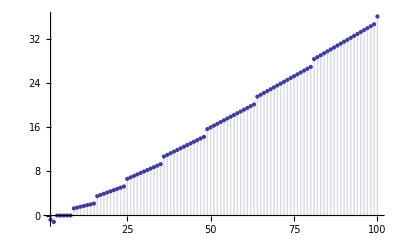

```mathematica
DiscretePlot[P2b[n],{n,2,100}]
```

```mathematica
FullSimplify[-n+FractionalPart[√n]^2+2 n ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu+n Log[4]+n Log[n]-2 n Log[Floor[√n]]+2 ∑_(a=2)^Floor[√n] FractionalPart[n/a]]
```

FractionalPart[√n]^2+n (-1+2 ∫_2^Floor[√n] FractionalPart[u]/u^2 ⅆu+Log[4]+Log[n]-2 Log[Floor[√n]])+2 ∑_(a=2)^Floor[√n] FractionalPart[n/a]

```mathematica
--------------------------------------------------------------------
```

```mathematica
PP[n_] :=Integrate[ (FractionalPart[x])/x^2,{x,2,n}]
```

```mathematica
PP[n]
```

```mathematica
∫_2^n z^-2 FractionalPart[z]ⅆz
```

∫_2^n FractionalPart[z]/z^2 ⅆz

```mathematica
Integrate[ z^(a-1)FractionalPart[z]]
```

Integrate::argmu: Integrate called with 1 argument; 2 or more arguments are expected.

```mathematica
Integrate[z^(-1+a) FractionalPart[z],z]
```

∫z^(-1+a) FractionalPart[z]ⅆz

```mathematica
N[Integrate[z^-2 FractionalPart[z],{z,2,10}]]
```

0.18047

```mathematica
FF[z_,a_] := (z^a FractionalPart[z])/a - z^(a+1)/(a(a+1))
```

```mathematica
FF2[z_, z2_, a_] := FF[z2,a] - FF[z,a]
```

```mathematica
FF2[2,10,2]
```

-496/3

```mathematica
Integrate[(x-1)/x^2,{x,1,2}]
```

-1/2+Log[2]

```mathematica
Sum[ Integrate[(x-j)/x^2,{x,j,j+1}],{j,2,n-1}]
```

Piecewise[{{1/3 (-1-3 Log[2]+3 Log[3]), n==3}, {1/2 (3-2 EulerGamma-2 Log[Pochhammer[2,-2+n]]+2 Log[Pochhammer[3,-2+n]]-2 PolyGamma[0,1+n]), True}}]

```mathematica
N[PP[80]]
```

0.2234

```mathematica
PQ[n_] := Piecewise[{{1/3 (-1-3 Log[2]+3 Log[3]), n==3}, {1/2 (3-2 EulerGamma-2 Log[Pochhammer[2,-2+n]]+2 Log[Pochhammer[3,-2+n]]-2 PolyGamma[0,1+n]), True}}]
```

```mathematica
N[PQ[4]]
```

0.109814

```mathematica
PQQ[n_] :=1/2 (3-2 EulerGamma-2 Log[Pochhammer[2,-2+n]]+2 Log[Pochhammer[3,-2+n]]-2 PolyGamma[0,1+n])
```

N::argt: N called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
N[PQQ[4]]
```

0.109814

```mathematica
Expand[1/2 (3-2 EulerGamma-2 Log[Pochhammer[2,-2+n]]+2 Log[Pochhammer[3,-2+n]]-2 PolyGamma[0,1+n])]
```

```mathematica
FullSimplify[3/2-EulerGamma-Log[Pochhammer[2,-2+n]]+Log[Pochhammer[3,-2+n]]-PolyGamma[0,1+n]]
```

3/2-HarmonicNumber[n]-Log[2 Gamma[n]]+Log[Gamma[1+n]]

```mathematica
PR[n_] := 3/2-HarmonicNumber[n]-Log[2 Gamma[n]]+Log[Gamma[1+n]]
```

```mathematica
N[PR[4]]
```

0.109814

```mathematica
N[Integrate[ (FractionalPart[x])/x^2,{x,2,4}]]
```

0.109814

```mathematica
----------------------------------------
```

```mathematica
H1[n_] := Integrate[ 1, {x,1,n},{y,1,n/x}] - Sum[ 1, {x,2,n},{y,2,n/x}]
```

```mathematica
N[H1[100]]
```

78.517

```mathematica
Ha[n_]:=n Log[n]-n+1 - (-n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (1/2+ Log[n]-Log[2]-Integrate[ (FractionalPart[x])/x^2,{x,2,n}])))
```

```mathematica
N[Ha[100]]
```

78.517

```mathematica
Expand[n Log[n]-n+1 - (-n+1 -Sum[FractionalPart[n/x],{x,2,n}]+(n (1/2+ Log[n]-Log[2]-Integrate[ (FractionalPart[x])/x^2,{x,2,n}])))]
```

-n/2+n ∫_2^n FractionalPart[x]/x^2 ⅆx+n Log[2]+∑_(x=2)^n FractionalPart[n/x]

```mathematica
Hb[n_] := -n/2+n ∫_2^n FractionalPart[x]/x^2 ⅆx+n Log[2]+∑_(x=2)^n FractionalPart[n/x]
```

```mathematica
Hc[n_] := -n/2+n Log[2]+∑_(x=2)^n FractionalPart[n/x]+n(3/2-HarmonicNumber[n]-Log[2 Gamma[n]]+Log[Gamma[1+n]])
```

```mathematica
N[Hc[100]]
```

78.517

```mathematica
Expand[-n/2+n Log[2]+∑_(x=2)^n FractionalPart[n/x]+n(3/2-HarmonicNumber[n]-Log[2 Gamma[n]]+Log[Gamma[1+n]])]
```

```mathematica
FullSimplify[n-n HarmonicNumber[n]+n Log[2]-n Log[2 Gamma[n]]+n Log[Gamma[1+n]]+∑_(x=2)^n FractionalPart[n/x]]
```

```mathematica
Hd[n_] :=n (1-HarmonicNumber[n]-Log[Gamma[n]]+Log[Gamma[1+n]])+∑_(x=2)^n FractionalPart[n/x]
```

```mathematica
N[Hd[100]]
```

78.517

```mathematica
FullSimplify[ Log[2]- Log[2Gamma[n]]]
```

-Log[Gamma[n]]

```mathematica
---------------------------------------------------------
```

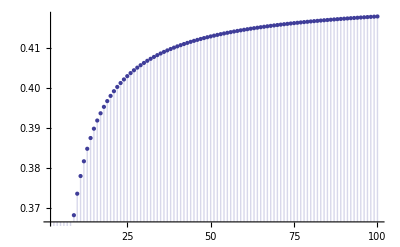

```mathematica
DiscretePlot[1-HarmonicNumber[n]-Log[Gamma[n]]+Log[Gamma[1+n]],{n,2,100}]
```